## functions

```mathematica
squeezeArr[array_]:=ArrayReshape[array,Dimensions[array]~DeleteCases~1];
```

## slices in all three directions

### Variables

```mathematica
div=80;
nDim=3;
alpha=0;
divLst=ConstantArray[div,nDim];
coordLst=Table[id/div,{id,0,div-1}];
coordLstFull=Table[id/div,{id,0,div}];
itNum=2000;
seed=1000;
mSize=4;
n=1;
fMod="memLayers";
fMod="";
fExt=jld2Type;
attrLst=attrLstBase;
valLst={nDim,mSize,divLst,itNum,seed};
If[alpha≠0,
valLst=valLst~Join~{NumberForm[alpha,{2,1}]};
attrLst=attrLst~Join~{"alpha"};]
attrLstDim={"dim"}~Join~attrLst;
attrLstDimLev=attrLstDim~Join~{"n"};
valLstLev=valLst~Join~{n};
(*valLstLev={nDim,mSize,divLst,itNum,seed,n};*)
```

```mathematica
alpha
```

0.4

```mathematica
{aLstTmp,vLstTmp}=fAttrValFunc[mSize,divLst,itNum,seed,nDim,"alpha"->alpha]
```

{{dim,N,param_divide,instanceNum,seed,alpha},{3,10,{80,80,80},500,1000,0.4}}

```mathematica
vLstTmp
```

{3,10,{80,80,80},500,1000,0.4}

```mathematica
avLstTmp
```

fAttrValFunc[10,{80,80,80},500,1000,3,0.4→0.4]

```mathematica
valLst
```

{3,10,{80,80,80},10,1000,1.0}

```mathematica
colorSch="Warm";
```

```mathematica
xyLab=MaTeX[#<>"/2\\pi",Magnification->labMag]&/@{"\\theta_1","\\theta_2"};
xyzLab=MaTeX[#<>"/2\\pi",Magnification->labMag]&/@{"\\theta_1","\\theta_2","\\theta_3"};
```

```mathematica
xyzLab
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Ohdraw.niL\Google_drive\Programming\Julia\Modules

```mathematica
valLst
```

{3,4,{64,64,64},10,1000}

```mathematica
fNameFun["deg_GOE_3d_full",attrLstDim,valLst,"",jldType]
```

deg_GOE_3d_full_dim_3_N_10_param_divide_[64, 64, 64]_instanceNum_100_seed_1000.jld

```mathematica
filename="deg_GOE_3d_full_dim_3_N_4_param_divide_[80, 80]_instanceNum_2_seed_1000.jld";
```

```mathematica
filename3d="deg_GOE_3d_full_dim_3_N_4_param_divide_[80, 80, 80]_instanceNum_100_seed_1000.jld";
```

```mathematica
fNameArr3d="parityArr_dim_3_N_4_param_divide_[80, 80, 80]_instanceNum_100_seed_1000.jld2";
```

```mathematica
filename3d=fNameFun["deg_GOE_3d_full",attrLstDim,valLst,fMod,jldType];
fNameArr3d=fNameFun["parityArr",attrLstDim,valLst,fMod,jld2Type];
fNameCorr3d=fNameFun["parityCorr_GOE",attrLstDim,valLst,fMod,jld2Type];
```

```mathematica
fNameCorrAvg=fNameFun["parityCorrAvg",attrLstDim,valLst,fMod,jld2Type];
fNameCorrStd=fNameFun["parityCorrStd",attrLstDim,valLst,fMod,jld2Type];
```

```mathematica
fNameCorr3d="parityCorr_GOE_dim_3_N_4_param_divide_[80, 80, 80]_instanceNum_100_seed_1000.jld2";
```

```mathematica
posLocLst=ExternalEvaluate[sessJul,"load("<>Py[Directory[]<>"\\"<>filename]<>",\"posLocLst\")"];
```

```mathematica
posLocLst3d=ExternalEvaluate[sessJul,"load("<>Py[Directory[]<>"\\"<>filename3d]<>",\"posLocLst\")"];
negLocLst3d=ExternalEvaluate[sessJul,"load("<>Py[Directory[]<>"\\"<>filename3d]<>",\"negLocLst\")"];
posLocLst3d1=Map[Transpose,posLocLst3d,{ArrayDepth[posLocLst3d]-1}];
```

```mathematica
Dimensions[posLocLst3d1]
```

{100,3,10,64}

```mathematica
Clear[parityCorrLst,parityCorrLst1]
```

```mathematica
parity2dLst=ExternalEvaluate[sessJul,"load("<>Py[Directory[]<>"\\"<>filename3d]<>",\"parity2dLst\")"];
```

```mathematica
parity2dArr=ExternalEvaluate[sessJul,"load("<>Py[Directory[]<>"\\"<>fNameArr3d]<>",\"parity2dArr\")"];
parity2dArr1=reverseDims[parity2dArr];
```

```mathematica
parity2dArr1//Dimensions
```

{10,3,80,80,10}

```mathematica
mag2dArr//Dimensions
```

{100,3,10}

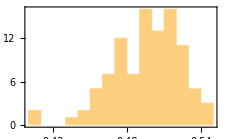

```mathematica
Histogram[mag2dArr⟦All,1,4⟧,12,"PDF",BaseStyle->texStyle,Frame->True,ImageSize->8cm]
```

```mathematica
.
```

```mathematica
Clear[posLocLst3d];
```

```mathematica
parityCorrLst=ExternalEvaluate[sessJul,"load("<>Py[Directory[]<>"\\"<>fNameCorr3d]<>",\"parityCorr\")"];
parityCorrLst1=reverseDims[parityCorrLst];
parityCorrAvg=Total[parityCorrLst1,{1}]/itNum/div^2;
parityCorrStd=StandardDeviation[parityCorrLst1/div^2];
```

```mathematica
parityCorrAvgRaw=readJuliaVar[fNameCorrAvg,"zacCorrAvg"];
parityCorrStdRaw=readJuliaVar[fNameCorrStd,"zacCorrStd"];
```

```mathematica
parityCorrAvg=reverseDims[parityCorrAvgRaw]/div^2/π^2;
parityCorrStd=reverseDims[parityCorrStdRaw]/div^2/π^2;
```

```mathematica
parityCorrAvg⟦1,1,1,1⟧
```

```mathematica
parityCorrAvg1//Dimensions
```

{3,80,80,4}

```mathematica
posLocLst3d1=Map[Transpose,posLocLst3d,{ArrayDepth[posLocLst3d]-1}];
```

```mathematica
parityCorrDat=Table[{coordLst⟦x⟧,coordLst⟦y⟧,Re[parityCorrLstSum⟦1,x,y,1⟧]/div^2/π/itNum},{x,1,div},{y,1,div}];
```

### Single instance

```mathematica
it=1;pdim=2;
xyLabP=Delete[xyzLab,pdim];
```

```mathematica
xyLabP
```

{-Graphics-,-Graphics-}

```mathematica
xyzLab
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
n
```

4

#### Puddles

```mathematica
0.0==0
```

True

```mathematica
EvenQ[0.]
```

False

```mathematica
NumberForm[0.0,{1,0}]
```

0.

```mathematica
NumberForm[0.0,{1,0}]mathematica
```

```mathematica
NumberForm[0.0,{2,1}]
```

0.0

```mathematica
tkLst
```

{{0.5,0.},{13.3,0.2},{26.1,0.4},{38.9,0.6},{51.7,0.8},{64.5,1.}}

```mathematica
0.2 0
```

0.

```mathematica
tkLst⟦-1,2⟧
```

1.

```mathematica
tkLst=Table[rat=0.2ii;{0.5+div rat,NumberForm[rat,2]},{ii,0,5}];
tkLst⟦1,2⟧=0;tkLst⟦-1,2⟧=1;
pltPudLstNoWr=Table[paritySample=Re[parity2dArr1⟦it,pdim,All,All,n⟧]/π;
xyLabP=Delete[xyzLab,pdim];
MatrixPlot[paritySampleᵀ,FrameLabel->Reverse[xyLabP],PlotRangePadding->None,FrameTicks->{{tkLst,None},{tkLst,None}},DataReversed->True,ColorFunction->"Monochrome",BaseStyle->texStyle,ImageSize->5cm],{pdim,1,nDim}];
```

```mathematica
pltPudLst=Table[paritySampleWr=Wrap0/@(Wrap0[Re[parity2dArr1⟦it,pdim,All,All,n⟧]/π]);
xyLabP=Delete[xyzLab,pdim];
paritySampleDat=Table[{coordLstFull⟦x⟧,coordLstFull⟦y⟧,paritySampleWr⟦x,y⟧},{x,1,div+1},{y,1,div+1}];
ListContourPlot[Flatten[paritySampleDat,1],ColorFunction->(GrayLevel[1-#]&),FrameLabel->xyLabP(*,PlotLegends->BarLegend[{GrayLevel[1-#]&,{0,1}},LabelStyle->texStyle,LegendMarkerSize->7cm]*),PlotRangePadding->None,BaseStyle->texStyle,ImageSize->5cm],{pdim,1,nDim}];
```

```mathematica
Export[fNameFun["puddle",attrLstDimLev,valLstLev,"puDim_"<>ToString[#],jpgType,True],pltPudLstNoWr⟦#⟧]&/@Table[d,{d,1,nDim}]
```

{puddle_dim_3_N_10_param_divide_80_80_80_instanceNum_10_seed_1000_alpha_1.0_n_4_puDim_1.jpg,puddle_dim_3_N_10_param_divide_80_80_80_instanceNum_10_seed_1000_alpha_1.0_n_4_puDim_2.jpg,puddle_dim_3_N_10_param_divide_80_80_80_instanceNum_10_seed_1000_alpha_1.0_n_4_puDim_3.jpg}

```mathematica
attrLstDimLev
```

{dim,N,param_divide,instanceNum,seed,alpha,n}

```mathematica
fNameFun["puddle",attrLstDimLev,valLstLev,"puDim_"<>ToString[#],epsType]&[1]
```

puddle_dim_3_N_10_param_divide_[64, 64, 64]_instanceNum_100_seed_1000_lev_4_puDim_1.eps

```mathematica
div
```

64

```mathematica
MatrixPlot[paritySampleWr,Frame->True,PlotRangePadding->Automatic,ImageSize->8cm,FrameTicks->{{Automatic,Automatic},{{{1-0.5,0},{20,20},{60,60},{65+0.5,2π}},Automatic}},DataReversed->True,BaseStyle->texStyle,ColorFunction->"Monochrome"]
```

-Graphics-

```mathematica
pltPudLstNoWr⟦1⟧
```

-Graphics-

```mathematica
alst={1,2,3};
blst=alst;
```

```mathematica
blst⟦2⟧=-3;
```

```mathematica
blst
```

{1,-3,3}

```mathematica
alst
```

{1,2,3}

#### Weyl loops

```mathematica
rotateSh={0,0,0};
grdMidSh={-0.5,-0.5,-1};
grdMidSh={0,0,0};
bndColorLst={Red,RGBColor[0,0.9,0],Blue};
marg=1;
```

```mathematica
bndColorLst={Red,RGBColor[0,0.9,0],Blue}
```

{RGBColor[1, 0, 0],RGBColor[0, 0.9, 0],RGBColor[0, 0, 1]}

```mathematica
isBndDim[coor_,div_,marg_]:=Module[{dim,isBnd=False},For[dim=1,dim≤3,dim++,If[coor⟦dim⟧≤marg||coor⟦dim⟧≥(div-marg),isBnd=True;Break[];]];
{isBnd,dim}];
```

```mathematica
posLocLst13d=posLocLst3d1⟦it,All,n,All⟧;
```

```mathematica
posLocLst13d⟦1,1⟧⟦1⟧
```

{30,1,1}

```mathematica
ptLstId3d=Table[Graphics3D[{If[isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦1⟧,bndColorLst⟦isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦2⟧⟧,Black],PointSize[If[isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦1⟧,Medium,Small]],Point[(RotateRight[posLocLst13d⟦dim,id3⟧⟦id1⟧,rotateSh⟦dim⟧]-RotateLeft[grdMidSh,dim-1])/div]}],{dim,1,3},{id3,1,Dimensions[posLocLst13d⟦dim⟧]⟦1⟧},{id1,1,Dimensions[posLocLst13d⟦dim,id3⟧]⟦1⟧}];
```

```mathematica
ptLstIdBlack3d=Table[Graphics3D[{If[isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦1⟧,Black,Black],PointSize[If[isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦1⟧,Small,Small]],Point[(RotateRight[posLocLst13d⟦dim,id3⟧⟦id1⟧,rotateSh⟦dim⟧]-RotateLeft[grdMidSh,dim-1])/div]}],{dim,1,3},{id3,1,Dimensions[posLocLst13d⟦dim⟧]⟦1⟧},{id1,1,Dimensions[posLocLst13d⟦dim,id3⟧]⟦1⟧}];
```

```mathematica
ptLstId2d=Table[Graphics[{Black,PointSize[Small],Point[Delete[(posLocLst13d⟦dim,id3⟧⟦id1⟧)/div,dimProj]]}],{dimProj,1,3},{dim,1,3},{id3,1,Dimensions[posLocLst13d⟦dim⟧]⟦1⟧},{id1,1,Dimensions[posLocLst13d⟦dim,id3⟧]⟦1⟧}];
```

```mathematica
ptLstId2d//Dimensions
```

{3,3,80}

```mathematica
ptLstId2d⟦1,1,1⟧
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pltWloopProjLst=Table[
xyLabP=Delete[xyzLab,d];Show[Flatten[ptLstId2d⟦d⟧],Frame->True,BaseStyle->texStyle,ImageSize->5cm,FrameLabel->xyLabP,PlotRangePadding->None],{d,1,3}];
```

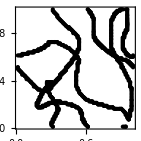

```mathematica
pltWloopProjLst⟦2⟧
```

```mathematica
Export[fNameFun["WloopProj",attrLstDimLev,valLstLev,"puDim_"<>ToString[#],epsType,True],pltWloopProjLst⟦#⟧]&/@{1,2,3};
```

```mathematica
valLst
```

{3,4,{80,80,80},100,1000}

```mathematica
Export["WloopProj_dim_"<>ToString[#]<>".eps",pltWloopProjLst⟦#⟧]&/@{1,2,3};
```

```mathematica
GraphicsGrid[Map[Show[#,Axes->True,AxesLabel->xyzLab,BaseStyle->texStyle,PlotRange->Full]&,{{ptLstId3d⟦3,All⟧,ptLstId3d⟦2,All⟧},{ptLstId3d⟦1,All⟧,Flatten[ptLstId3d]}},{2}]]
```

-Graphics-

```mathematica
pltWloop3d=Show[Flatten[ptLstIdBlack3d],Axes->True,AxesLabel->xyzLab,BaseStyle->texStyle,PlotRange->Full,ImageSize->8cm,PlotRangePadding->None]
```

-Graphics3D-

```mathematica
pltWloop3d=Show[Flatten[ptLstId3d],Axes->True,AxesLabel->xyzLab,BaseStyle->texStyle,PlotRange->Full,ImageSize->8cm,PlotRangePadding->None]
```

-Graphics3D-

```mathematica
Show[pltWloop3d,Boxed->False]
```

```mathematica
fTmp=fNameFun["Wloop3d",attrLstDimLev,valLstLev,"",epsType,True]
```

Wloop3d_dim_3_N_10_param_divide_64_64_64_instanceNum_100_seed_1000_lev_4.eps

```mathematica
StringDelete[fTmp,{" ","[","]"}]
```

Wloop3d_dim_3_N_10_param_divide_64_64_64_instanceNum_100_seed_1000_lev_4.eps

```mathematica
Export[fNameFun["Wloop3d",attrLstDimLev,valLstLev,"",epsType,True],pltWloop3d];
```

```mathematica
pltWloop3d=Show[Flatten[ptLstId3d],Axes->True,AxesLabel->xyzLab,BaseStyle->texStyle,PlotRange->Full,ImageSize->5cm,PlotRangePadding->None,ViewPoint->{0,-Infinity,0}]
```

-Graphics3D-

```mathematica
GraphicsGrid[{{Show[ptLstId3d⟦3,All⟧,Axes->True,AxesLabel->xyzLab,PlotRange->Full],Show[ptLstId3d⟦2,All⟧,Axes->True,AxesLabel->xyzLab,PlotRange->Full]},{Show[ptLstId3d⟦1,All⟧,Axes->True,AxesLabel->xyzLab,PlotRange->Full],Show[Flatten[ptLstId3d],Axes->True,AxesLabel->xyzLab,PlotRange->Full]}}]
```

-Graphics-

### Correlation

```mathematica
marg=5;
fitMod=NonlinearModelFit[{coordLst,parityCorrAvg⟦pdim,All,1,n⟧}ᵀ⟦1;;marg⟧,c( Exp[-x/a]+Exp[-(1-x)/a])+b,{a,b,c},x,Weights->1/(parityCorrStd⟦pdim,All,1,n⟧⟦1;;marg⟧)^2,VarianceEstimatorFunction->(1&)];
```

```mathematica
fitMod["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.00623278 | 0.00148366 | 4.20096 | 0.0522613
b | 2.47155 | 0.0587301 | 42.0832 | 0.000564176
c | 2.46641 | 0.106052 | 23.2565 | 0.00184378

```mathematica
fitMod["ParameterTableEntries"]
```

{{0.00623278,0.00148366,4.20096,0.0522613},{2.47155,0.0587301,42.0832,0.000564176},{2.46641,0.106052,23.2565,0.00184378}}

```mathematica
fitMod["ParameterTable"]nonlinearfitMod["ParameterTable"]
```

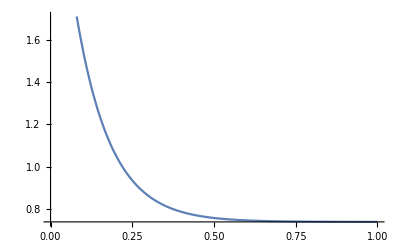

```mathematica
Plot[fitMod["Function"][x],{x,0,1}]
```

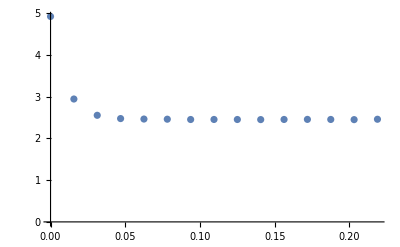

```mathematica
marg=15;
ListPlot[{coordLst,parityCorrAvg⟦pdim,All,1,n⟧}ᵀ⟦1;;marg⟧,PlotRange->All]
```

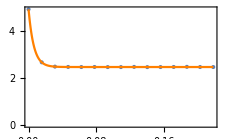

```mathematica
marg=15;
Show[ListPlot[{coordLstFull,Wrap0[parityCorrAvg⟦pdim,All,1,n⟧]}ᵀ⟦1;;marg⟧,PlotRange->Full],Plot[fitMod["Function"][x],{x,0,coordLstFull⟦marg⟧},PlotStyle->Orange,PlotRange->Full],BaseStyle->texStyle,Frame->True,FrameLabel->xyLabCorr1d,ImageSize->8cm]
```

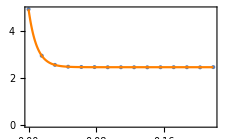

```mathematica
marg=15;
Show[ListPlot[{coordLstFull,Wrap0[parityCorrAvg⟦pdim,All,1,n⟧]}ᵀ⟦1;;marg⟧,PlotRange->All],Plot[fitMod["Function"][x],{x,0,coordLstFull⟦marg⟧},PlotStyle->Orange,PlotRange->All],BaseStyle->texStyle,Frame->True,FrameLabel->xyLabCorr1d,ImageSize->8cm]
```

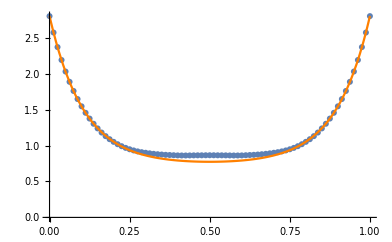

```mathematica
marg=81;
Show[ListPlot[{coordLstFull,Wrap0[parityCorrAvg⟦1,All,1,1⟧]}ᵀ⟦1;;marg⟧],Plot[fitMod["Function"][x],{x,0,coordLstFull⟦marg⟧},PlotStyle->Orange,PlotRange->All]]
```

```mathematica
fitMod["Function"]
```

0.739012+2.06514 ⅇ^(-9.41033 #1)&

```mathematica
paritySampleWr=Wrap0/@(Wrap0[Re[parity2dArr⟦1,All,All,3,1⟧]/π]);
paritySampleDat=Table[{coordLstFull⟦x⟧,coordLstFull⟦y⟧,paritySampleWr⟦x,y⟧},{x,1,div+1},{y,1,div+1}];
ListContourPlot[Flatten[paritySampleDat,1],ColorFunction->(GrayLevel[1-#]&),FrameLabel->xyLab,PlotLegends->BarLegend[{GrayLevel[1-#]&,{0,1}},LabelStyle->texStyle,LegendMarkerSize->7cm],PlotRangePadding->None,BaseStyle->texStyle,ImageSize->8cm]
```

-Graphics-

```mathematica
x
```

x

```mathematica
pdim=1;
parityCorrDat=Table[{coordLstFull⟦x⟧,coordLstFull⟦y⟧,(Wrap0/@Wrap0[parityCorrAvg⟦pdim,All,All,n⟧])⟦x,y⟧},{x,1,div+1},{y,1,div+1}];
```

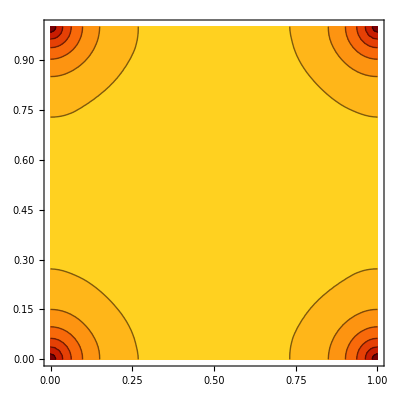

```mathematica
colorSch="Warm";
marg=div+1;
thckNum=6;
pltCorrFull=Show[ListContourPlot[Flatten[parityCorrDat⟦1;;marg,1;;marg⟧,1],PlotRangePadding->None,ColorFunction->ColorData[{colorSch,{1,0}}](*,PlotLegends->BarLegend[{ColorData[{colorSch,{1,0}}],{0,1}},LabelStyle->texStyle,LegendMarkerSize->6cm]*),BaseStyle->texStyle,ImageSize->{Automatic,7cm},FrameLabel->xyLab,PlotRange->All]]
```

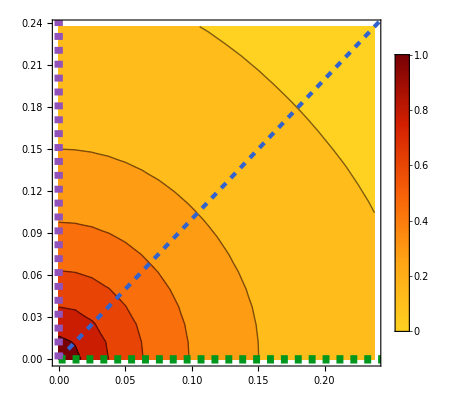

```mathematica
colorSch="Warm";
marg=20;
thckNum=6;
thck=AbsoluteThickness[thckNum];
thc2=AbsoluteThickness[thckNum/2];
pltCorrQuarter=Show[ListContourPlot[Flatten[parityCorrDat⟦1;;marg,1;;marg⟧,1],PlotRangePadding->None,ColorFunction->ColorData[{colorSch,{1,0}}],PlotLegends->BarLegend[{ColorData[{colorSch,{1,0}}],{0,1}},LabelStyle->texStyle,LegendMarkerSize->6cm],BaseStyle->texStyle,ImageSize->{Automatic,7cm},FrameLabel->xyLab,PlotRange->All],Graphics[{colorLst⟦3⟧,thc2,Dashed,CapForm["Butt"],Line[{{0,0},{0.3,0.3}}]}],Graphics[{colorLst⟦5⟧,thck,Dashed,CapForm["Butt"],Line[{{0,0},{0.3,0}}]}],Graphics[{colorLst⟦6⟧,thck,Dashed,CapForm["Butt"],Line[{{0,0},{0,0.3}}]}]]
```

```mathematica
Export[fNameFun["parityCorrQuarter",attrLstDimLev,valLstLev,"",pdfType,True],pltCorrQuarter]
```

parityCorrQuarter_dim_3_N_4_param_divide_80_80_80_instanceNum_2000_seed_1000_n_1.pdf

```mathematica
(*Export["parityCorrQuarter_n4_it100.eps",pltCorrQuarter]*)
```

parityCorrQuarter_n4_it100.eps

```mathematica
Export[fNameFun["parityCorrFull",attrLstDimLev,valLstLev,"",epsType,True],pltCorrFull];
```

```mathematica
(*Export["parityCorrFull_n4_it100.eps",pltCorrFull]*)
```

parityCorrFull_n4_it100.eps

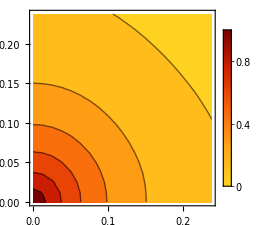

```mathematica
colorSch="Warm";
marg=20;
ListContourPlot[Flatten[parityCorrDat⟦1;;marg,1;;marg⟧,1],PlotRangePadding->None,ColorFunction->ColorData[{colorSch,{1,0}}],PlotLegends->BarLegend[{ColorData[{colorSch,{1,0}}],{0,1}},LabelStyle->texStyle,LegendMarkerSize->7cm],BaseStyle->texStyle,ImageSize->8cm,FrameLabel->xyLab,PlotRange->All]
```

```mathematica
colorSch="Warm";
marg=20;
ListContourPlot[Flatten[parityCorrDat⟦1;;marg,1;;marg⟧,1],PlotRangePadding->None,ColorFunction->ColorData[{colorSch,{0,1}}],PlotLegends->BarLegend[{colorSch,{0,1}},LabelStyle->texStyle,LegendMarkerSize->6cm],BaseStyle->texStyle,ImageSize->8cm,FrameLabel->xyLab,PlotRange->All]
```

```mathematica
xyLabCorr1d=MaTeX[#,Magnification->labMag]&/@{"\\left| \\theta \\right| / 2\\pi","F_{n,3} \\left( \\left| \\theta \\right| \\right)"};
```

```mathematica
parityCorrXerr=makeDataErr[parityCorrAvg⟦pdim,All,1,n⟧,parityCorrStd⟦pdim,All,1,n⟧];
```

```mathematica
parityCorrAvg//Dimensions
```

{3,64,64,30}

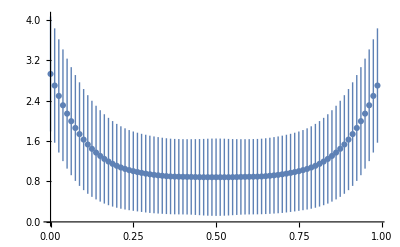

```mathematica
ListPlot[{coordLst,parityCorrX}ᵀ,]
```

```mathematica
Join[{#},{dataThick}]&/@colorLst⟦{3,5,6,7}⟧
```

{{RGBColor[0.192157, 0.388235, 0.807843],AbsoluteThickness[1]},{RGBColor[0., 0.596078, 0.109804],AbsoluteThickness[1]},{RGBColor[0.567426, 0.32317, 0.729831],AbsoluteThickness[1]},{RGBColor[0., 0.588235, 0.705882],AbsoluteThickness[1]}}

```mathematica
colorLst⟦1;;10⟧
```

{GrayLevel[0],RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074]}

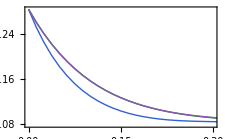

```mathematica
pltCorr1d=ListLinePlot[{{coordLst,Diagonal[parityCorrAvg⟦pdim,All,All,n⟧]}ᵀ,{coordLst,parityCorrAvg⟦pdim,All,1,n⟧}ᵀ,{coordLst,parityCorrAvg⟦pdim,1,All,n⟧}ᵀ},PlotStyle->(Join[{#},{dataThick}]&/@colorLst⟦{3,5,6,7}⟧),PlotRange->{{0,0.3},All},Frame->True,FrameLabel->xyLabCorr1d,BaseStyle->texStyle,ImageSize->8cm,PlotRangePadding->None]
```

```mathematica
Export[fNameFun["parityCorr1d",attrLstDimLev,valLstLev,"",pdfType,True],pltCorr1d];
```

```mathematica
(*Export["parityCorr1d.eps",pltCorr1d];*)
```

```mathematica
parityCorrLst//Dimen
```

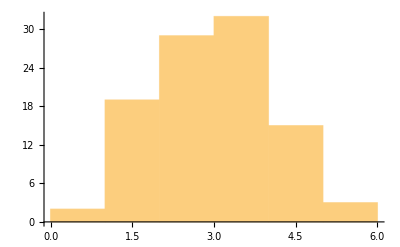

```mathematica
Histogram[parityCorrLst1⟦All,pdim,1,1,n⟧/div^2]
```

```mathematica
marg=15;
fitMod=NonlinearModelFit[{coordLst,parityCorrAvg⟦pdim,All,1,n⟧}ᵀ⟦1;;marg⟧,c( Exp[-x/a]+Exp[-(1-x)/a])+b,{a,b,c},x];
```

```mathematica
fitMod["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0205658 | 0.0000685246 | 300.123 | 1.26036×10^-24
b | 2.43554 | 0.00120312 | 2024.35 | 1.42218×10^-34
c | 2.45442 | 0.00373593 | 656.976 | 1.04168×10^-28

```mathematica
colorLst⟦1;;10⟧
```

{GrayLevel[0],RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074]}

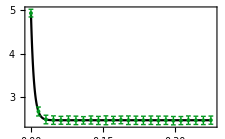

```mathematica
marg=25;
pltCorr1dXfit=Show[Plot[fitMod["Function"][x],{x,0,coordLstFull⟦marg⟧},PlotStyle->colorLst⟦1⟧,PlotRange->All],ListPlot[{coordLstFull,Wrap0[parityCorrXerr]}ᵀ⟦1;;marg⟧,PlotMarkers->{Automatic,Tiny},PlotStyle->colorLst⟦5⟧,IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->fenceW/4|>],ImageSize->8cm,Frame->True,FrameLabel->xyLabCorr1d,BaseStyle->texStyle,PlotRangePadding->None,Axes->False]
```

```mathematica
Export[fNameFun["parityCorr1dXfit",attrLstDimLev,valLstLev,"",epsType,True],pltCorr1dXfit];
```

```mathematica
(*Export["parityCorr1dXfit.eps",pltCorr1dXfit];*)
```

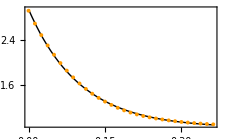

```mathematica
marg=30;
Show[Plot[fitMod["Function"][x],{x,0,coordLstFull⟦marg⟧},PlotStyle->{colorLst⟦1⟧,dataThick},PlotRange->All],ListPlot[{coordLstFull,Wrap0[parityCorrAvg⟦pdim,All,1,n⟧]}ᵀ⟦1;;marg⟧,PlotMarkers->{Automatic,Tiny},PlotStyle->colorLst⟦4⟧,IntervalMarkers->"Fences",IntervalMarkersStyle-><|"FenceWidth"->fenceW/4|>],ImageSize->8cm,Frame->True,FrameLabel->xyLabCorr1d,BaseStyle->texStyle,PlotRangePadding->None,Axes->False]
```

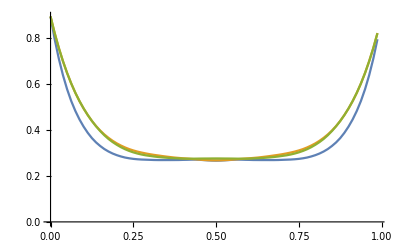

```mathematica
ListLinePlot[{{coordLst,Diagonal[parityCorrLstSum⟦1,All,All,1⟧]/div^2/itNum/π}ᵀ,{coordLst,parityCorrLstSum⟦1,All,1,1⟧/div^2/itNum/π}ᵀ,{coordLst,parityCorrLstSum⟦1,1,All,1⟧/div^2/itNum/π}ᵀ}]
```

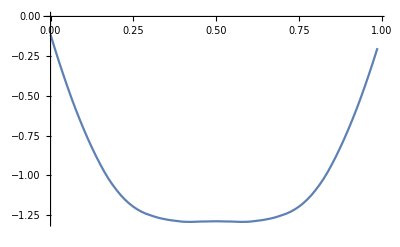

```mathematica
ListLinePlot[{{coordLst,Log[parityCorrLstSum⟦1,1,All,1⟧/div^2/itNum/π]}ᵀ}]
```

```mathematica
colorSch="Warm";
marg=20;
Show[ListContourPlot[Flatten[parityDat⟦1;;20,1;;20⟧,1],ColorFunction->ColorData[{colorSch,{0,1}}],PlotLegends->BarLegend[{colorSch,{0,1}},LabelStyle->texStyle,LegendMarkerSize->6cm],FrameLabel->xyLab],BaseStyle->texStyle,ImageSize->8cm]
```

```mathematica
Clear[parity2dLst]
```

```mathematica
parityCorrLst1=Transpose[parityCorrLst⟦1⟧,{5,4,3,2,1}];
```

```mathematica
parityCorrLst1//Dimensions
```

{100,3,80,80,4}

```mathematica
parityCorrSum=Total[parityCorrLst1,{1}];
```

```mathematica
parityCorrSum//Dimensions
```

{3,80,80,4}

```mathematica
parityCorrLst1⟦1,1,1,1;;10,All⟧
```

{{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.}}

```mathematica
parityArrDat=Table[{coordLst⟦x⟧,coordLst⟦y⟧,Re[parity2dArr⟦1⟧⟦1,x,y,1,1⟧/π]},{x,1,div},{y,1,div}];
```

```mathematica
parity2dArr⟦1⟧⟦1,1,1,1,1⟧
```

<|re→0.,im→0.|>

```mathematica
parityCorrLst1⟦1,1,1,1,1⟧
```

0.

```mathematica
ListContourPlot[{coordLst,coordLst,parityArrDat},PlotLegends->Automatic]
```

ListContourPlot::arrayerr: {{0.,0.0125,0.025,0.0375,0.05,0.0625,0.075,0.0875,0.1,0.1125,«70»},{0.,0.0125,0.025,0.0375,0.05,0.0625,0.075,0.0875,0.1,0.1125,«70»},{«1»}} must be a valid array.

ListContourPlot[{1},PlotLegends→Automatic]
 |  |  |  |

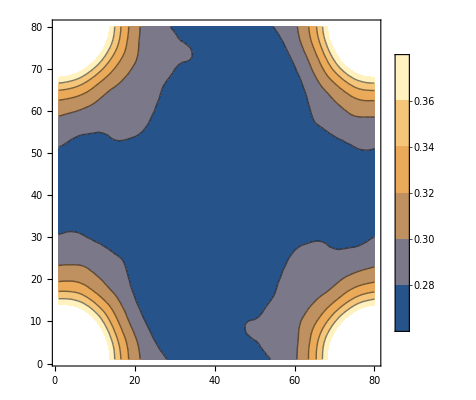

```mathematica
ListContourPlot[Re[parityCorrLstSum⟦1,All,All,1⟧/div^2/itNum/π],PlotLegends->Automatic]
```

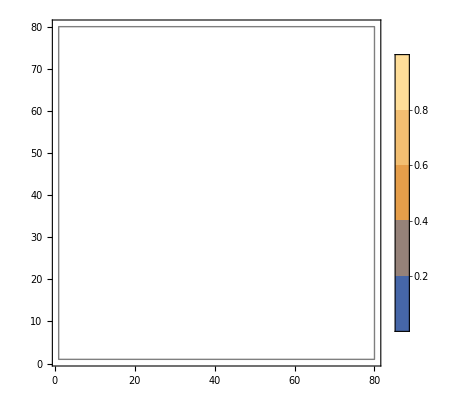

```mathematica
ListContourPlot[{coordLst,coordLst,Re[parityCorrSum⟦1,All,All,2⟧/div^2/π/itNum]},PlotLegends->Automatic]
```

```mathematica
parityCorr=Sum[parity2dLst1⟦it,1,x,y⟧*RotateLeft[parity2dLst1⟦it,1⟧,{x,y}-1],{x,1,div},{y,1,div},{it,1,itNum}];
```

$Aborted

```mathematica
parityCorr=ConstantArray[0,{div,div}];
itNumCut=10;
For[it=1,it≤itNumCut,it++,
For[x=1,x≤div,x++,For[y=1,y≤div,y++,parityCorr=parityCorr+parity2dLst1⟦it,1,x,y⟧*RotateLeft[parity2dLst1⟦it,1⟧,{x,y}-1]]]]
```

$Aborted

```mathematica
parityCorr⟦2,2⟧/div^2/π/itNum
```

0.793144+0. ⅈ

```mathematica
itNum
```

100

```mathematica
coordLst=Table[id/div,{id,0,div-1}];
```

```mathematica
parityDat=Table[{coordLst⟦x⟧,coordLst⟦y⟧,Re[parityCorr⟦x,y⟧/div^2/π/itNum]},{x,1,div},{y,1,div}];
```

```mathematica
Dimensions[parityDat]
```

{80,80,3}

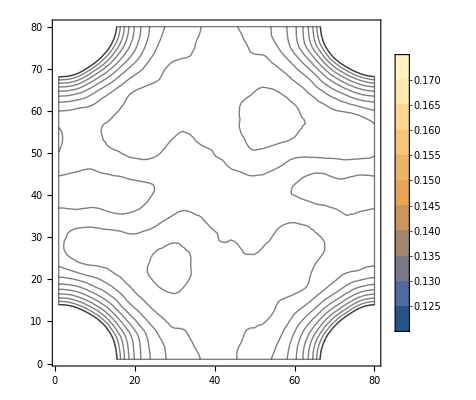

```mathematica
ListContourPlot[{coordLst,coordLst,Re[parityCorr/div^2/π/itNum]},PlotLegends->Automatic]
```

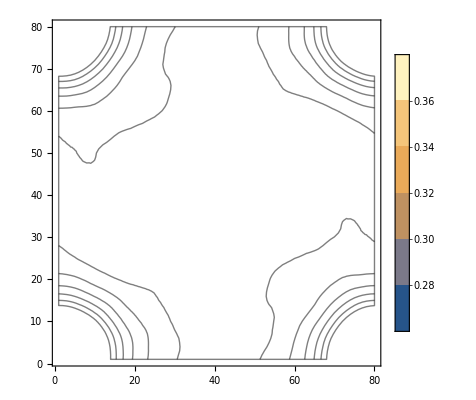

```mathematica
ListContourPlot[{coordLst,coordLst,Re[parityCorr/div^2/π/itNum]},PlotLegends->Automatic]
```

```mathematica
parityDatFl=Flatten[parityDat,1];
```

```mathematica
Dimensions[parityDatFl]
```

{6400,3}

```mathematica
ParityDatFl⟦1⟧
```

Part::partd: Part specification ParityDatFl⟦1⟧ is longer than depth of object.

ParityDatFl⟦1⟧

```mathematica
parityCorr⟦1,1⟧/div^2/π/itNum
```

0.891996+0. ⅈ

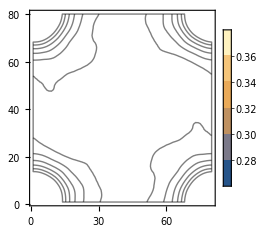

```mathematica
Show[ListContourPlot[{coordLst,coordLst,parityCorr/div^2/π/itNum},PlotLegends->Automatic],ImageSize->8cm]
```

```mathematica
xyLab=MaTeX[#,Magnification->labMag]&/@{"\\theta_1","\\theta_2"}
```

{-Graphics-,-Graphics-}

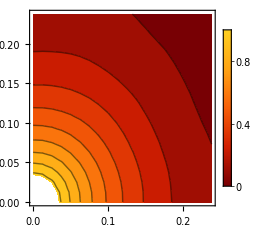

```mathematica
colorSch="Warm";
marg=20;
Show[ListContourPlot[Flatten[parityDat⟦1;;20,1;;20⟧,1],ColorFunction->ColorData[{colorSch,{0,1}}],PlotLegends->BarLegend[{colorSch,{0,1}},LabelStyle->texStyle,LegendMarkerSize->6cm],FrameLabel->xyLab],BaseStyle->texStyle,ImageSize->8cm]
```

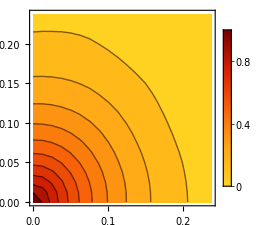

```mathematica
colorSch="Warm";
marg=20;
Show[ListContourPlot[Flatten[parityDat⟦1;;marg,1;;marg⟧,1],ColorFunction->ColorData[{colorSch,{1,0}}],PlotRange->All,Contours->10,PlotRangePadding->None,PlotLegends->Placed[BarLegend[{ColorData[{colorSch,{1,0}}],{0,1}},LabelStyle->texStyle,LegendMarkerSize->6cm,LegendMargins->0],Right],FrameLabel->xyLab],BaseStyle->texStyle,ImageSize->8cm]
```

```mathematica
colorSch="Warm";
Show[ListContourPlot[parityDatFl,ColorFunction->ColorData[{colorSch,{1,0}}],PlotRange->All,Contours->10,PlotRangePadding->None,PlotLegends->Placed[BarLegend[{ColorData[{colorSch,{1,0}}],{0,1}},LabelStyle->texStyle,LegendMarkerSize->6cm,LegendMargins->0],Right],FrameLabel->xyLab],BaseStyle->texStyle,ImageSize->8cm]
```

ListContourPlot::arrayerr: parityDatFl must be a valid array.

Show::gtype: ListContourPlot is not a type of graphics.

```mathematica
Show[ListContourPlot[parityDat,PlotLegends->Automatic],ImageSize->8cm]
```

-Graphics-

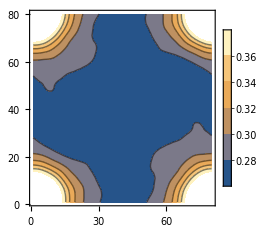

```mathematica
Show[ListContourPlot[parityCorr/div^2/π/itNum,PlotLegends->Automatic],ImageSize->8cm]
```

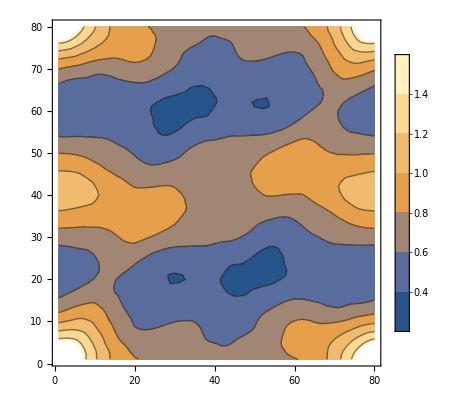

```mathematica
ListContourPlot[parityCorr/div^2/π,PlotLegends->Automatic]
```

```mathematica
testArr=Table[a+b,{a,1,3},{b,1,3}]
```

{{2,3,4},{3,4,5},{4,5,6}}

```mathematica
testArr//MatrixForm
```

(2 | 3 | 4
3 | 4 | 5
4 | 5 | 6)

```mathematica
RotateLeft[testArr,1]//MatrixForm
```

(3 | 4 | 5
4 | 5 | 6
2 | 3 | 4)

```mathematica
Det[{{3,4,5},{4,5,6},{2,3,4}}]
```

0

```mathematica
RotateLeft[testArr,{1,2}]//MatrixForm
```

(5 | 3 | 4
6 | 4 | 5
4 | 2 | 3)

```mathematica
Dimensions[parity2dLst]
```

{2,1,3,1,80,80,4,1}

```mathematica
coorLst=(Table[id,{id,1,div}]-1);
```

```mathematica
Show[ListContourPlot[{parity2dLst⟦1,1,1,1,All,All,1,1⟧/π},ColorFunction->GrayLevel,PlotLegends->Automatic],BaseStyle->texStyle,ImageSize->8cm]
```

-Graphics-

```mathematica
posLocLst1=posLocLst⟦All,All,1⟧;
```

```mathematica
posLocLst13d=posLocLst3d⟦2,1,All,1,All,1⟧;
```

```mathematica
HGOElst=ExternalEvaluate[sessJul,"load("<>Py[Directory[]<>"\\"<>filename]<>",\"H_GOElst_All\")"];
```

```mathematica
HGOElst3d=ExternalEvaluate[sessJul,"load("<>Py[Directory[]<>"\\"<>filename3d]<>",\"H_GOElst_All\")"];
```

```mathematica
HGOElst⟦1,1⟧//MatrixForm
```

(-2.19847+0. ⅈ | -1.22135+0. ⅈ | 0.0951445+0. ⅈ | 1.38417+0. ⅈ
-1.22135+0. ⅈ | 1.49402+0. ⅈ | 1.18278+0. ⅈ | -1.09101+0. ⅈ
0.0951445+0. ⅈ | 1.18278+0. ⅈ | -1.14362+0. ⅈ | 1.10858+0. ⅈ
1.38417+0. ⅈ | -1.09101+0. ⅈ | 1.10858+0. ⅈ | 0.494874+0. ⅈ)

```mathematica
HGOElst3d⟦1,1⟧//MatrixForm
```

(-2.19847+0. ⅈ | -1.22135+0. ⅈ | 0.0951445+0. ⅈ | 1.38417+0. ⅈ
-1.22135+0. ⅈ | 1.49402+0. ⅈ | 1.18278+0. ⅈ | -1.09101+0. ⅈ
0.0951445+0. ⅈ | 1.18278+0. ⅈ | -1.14362+0. ⅈ | 1.10858+0. ⅈ
1.38417+0. ⅈ | -1.09101+0. ⅈ | 1.10858+0. ⅈ | 0.494874+0. ⅈ)

```mathematica
Dimensions[posLocLst]
```

{3,80,4,1}

```mathematica
Dimensions[posLocLst3d]
```

{2,1,3,1,80,4}

```mathematica
Dimensions[posLocLst3d⟦2⟧]
```

{1}

```mathematica
posLocLst⟦2,1,10,1⟧
```

Part::partw: Part 10 of {{{{77,6},{79,26},{78,28},{76,70}}},{{{77,6},{75,11},{78,28},{76,70},{31,23},{79,26},{61,40},{60,63},{66,68},{34,70}}},{{{61,40},{5,49},{60,63},{61,68},{66,68},{75,11},{22,12},{31,23},{34,70},{47,73}}},{{{61,68},{22,12},{5,49},{47,73}}}} does not exist.

{1}⟦2,1,10,1⟧
 |  |  |  |

```mathematica
posLocLst⟦2,1,1,1⟧
```

{{77,6},{79,26},{78,28},{76,70}}

```mathematica
Dimensions[posLocLst⟦1,1,80,1⟧]
```

Part::partw: Part 80 of {{{{46,41},{53,49}}},{{{74,19},{72,40},{46,41},{53,49},{77,61},{3,66},{7,78},{55,37}}},{{{61,9},{74,19},{63,23},{55,37},{9,54},{7,78},{21,10},{72,40},{77,61},{3,66}}},{{{61,9},{21,10},{63,23},{9,54}}}} does not exist.

{5}

```mathematica
posLocLstFl=squeezeArr[posLocLst];
```

```mathematica
Dimensions[posLocLst]
```

{3,80,4,1}

```mathematica
posLocLst⟦1,1,1,1⟧
```

{{46,41},{53,49}}

```mathematica
Dimensions[posLocLstFl]
```

{3,80,4}

```mathematica
Dimensions[posLocLst]
```

{3,80,4,1}

```mathematica
Dimensions[posLocLst3d]
```

{3,1,80,4}

```mathematica
Dimensions[posLocLst1]
```

{3,80,1}

```mathematica
Dimensions[posLocLst1⟦1⟧]
```

{80,1}

```mathematica
posLocLst1Fl=ArrayReshape[posLocLst1,{3,80}];
```

```mathematica
Dimensions[posLocLst]
```

{3,80,4,1}

```mathematica
posLocLst1⟦1,1⟧
```

{{{46,41},{53,49}}}

```mathematica
posLocLst1Fl2=Flatten[#]&/@posLocLst1;
```

```mathematica
Dimensions[posLocLst1]
```

{3,80,1}

```mathematica
posLocLst1Fl⟦1⟧
```

{46,41,53,49,45,39,53,49,44,38,53,49,43,37,52,49,42,36,52,50,42,35,52,50,41,34,52,50,53,50,40,33,53,51,40,32,40,31,53,51,39,30,53,51,54,51,39,29,38,28,54,52,38,27,54,52,73,17,55,52,72,14,38,26,70,14,37,26,56,53,73,19,68,14,72,21,56,53,37,25}

```mathematica
posLocLst1⟦1,40,1,1⟧
```

{22,47}

```mathematica
Dimensions[posLocLst1⟦1,1⟧]
```

{1,2,2}

```mathematica
Dimensions[posLocLst1⟦1,40,1⟧]
```

{4,2}

```mathematica
id3=3;id1=2;dim=3;
RotateRight[{id3}~Join~posLocLst1⟦dim,id3,1⟧⟦id1⟧,dim-1]
```

{47,31,3}

```mathematica
marg=1;
```

```mathematica
coor
```

coor

```mathematica
div
```

80

### Weyl loops

```mathematica
isBndDim[coor_,div_,marg_]:=Module[{dim,isBnd=False},For[dim=1,dim≤3,dim++,If[coor⟦dim⟧≤marg||coor⟦dim⟧≥(div-marg),isBnd=True;Break[];]];
{isBnd,dim}];
```

```mathematica
coor⟦1⟧≤marg||coor⟦2⟧≤marg||coor⟦3⟧≤marg||(coor⟦1⟧≥(div-marg))||(coor⟦2⟧≥(div-marg))||(coor⟦3⟧≥(div-marg));
```

Part::partd: Part specification coor⟦1⟧ is longer than depth of object.

Part::partd: Part specification coor⟦2⟧ is longer than depth of object.

Part::partd: Part specification coor⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
B
```

B

```mathematica
isBndDim[{2,79,3},80,1]
```

{True,2}

```mathematica
posLocLst1⟦1,20,1⟧
```

{{64,15},{38,25},{69,26},{59,55}}

```mathematica
posLocLst1⟦1,1⟧⟦1⟧
```

{{46,41},{53,49}}

```mathematica
Dimensions[posLocLst1⟦2,20,1⟧]
```

{0}

```mathematica
posLocLst1⟦1,2,1⟧
```

{{45,39},{53,49}}

```mathematica
Dimensions[posLocLst13d⟦1,1⟧]⟦1⟧
```

4

```mathematica
Dimensions[posLocLst13d⟦1,20⟧]
```

{4,3}

```mathematica
colorLst={Red,Green,Blue};
```

```mathematica
RotateRight[{1,2,3},-1]
```

{2,3,1}

```mathematica
rotateSh={0,0,0};
```

```mathematica
grdMidSh={-0.5,-0.5,-1};
```

```mathematica
grdMidSh={0,0,0};
```

```mathematica
ptLstId3d=Table[Graphics3D[{If[isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦1⟧,colorLst⟦isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦2⟧⟧,Black],PointSize[If[isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦1⟧,Medium,Small]],Point[(RotateRight[posLocLst13d⟦dim,id3⟧⟦id1⟧,rotateSh⟦dim⟧]-RotateLeft[grdMidSh,dim-1])/div]}],{dim,1,3},{id3,1,Dimensions[posLocLst13d⟦dim⟧]⟦1⟧},{id1,1,Dimensions[posLocLst13d⟦dim,id3⟧]⟦1⟧}];
```

```mathematica
GraphicsGrid[{{Show[ptLstId3d⟦3,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full],Show[ptLstId3d⟦2,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]},{Show[ptLstId3d⟦1,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full],Show[Flatten[ptLstId3d],Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]}}]
```

-Graphics-

```mathematica
Show[Flatten[ptLstId3d],Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]
```

-Graphics3D-

```mathematica
ptLstId3d=Table[Graphics3D[{If[isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦1⟧,colorLst⟦isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦2⟧⟧,Black],PointSize[If[isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦1⟧,Medium,Small]],Point[(RotateRight[posLocLst13d⟦dim,id3⟧⟦id1⟧,rotateSh⟦dim⟧]-RotateLeft[grdMidSh,dim-1])/div]}],{dim,1,3},{id3,1,Dimensions[posLocLst13d⟦dim⟧]⟦1⟧},{id1,1,Dimensions[posLocLst13d⟦dim,id3⟧]⟦1⟧}];
```

```mathematica
GraphicsGrid[{{Show[ptLstId3d⟦3,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full],Show[ptLstId3d⟦2,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]},{Show[ptLstId3d⟦1,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full],Show[Flatten[ptLstId3d],Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]}}]
```

-Graphics-

```mathematica
ptLstId3d=Table[Graphics3D[{If[isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦1⟧,colorLst⟦isBndDim[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg]⟦2⟧⟧,Black],PointSize[If[isBnd[posLocLst13d⟦dim,id3⟧⟦id1⟧,div,marg],Medium,Small]],Point[(RotateRight[posLocLst13d⟦dim,id3⟧⟦id1⟧,rotateSh⟦dim⟧]-RotateLeft[grdMidSh,dim-1])/div]}],{dim,1,3},{id3,1,Dimensions[posLocLst13d⟦dim⟧]⟦1⟧},{id1,1,Dimensions[posLocLst13d⟦dim,id3⟧]⟦1⟧}];
```

```mathematica
GraphicsGrid[{{Show[ptLstId3d⟦3,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full],Show[ptLstId3d⟦2,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]},{Show[ptLstId3d⟦1,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full],Show[Flatten[ptLstId3d],Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]}}]
```

-Graphics-

```mathematica
Show[Flatten[ptLstId3d],Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]
```

-Graphics3D-

```mathematica
Show[Flatten[ptLstId3d],Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]
```

-Graphics3D-

```mathematica
Show[Flatten[ptLstId3d],Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]
```

-Graphics3D-

```mathematica
posLocLst1⟦1,1⟧
```

{{{46,41},{53,49}}}

```mathematica
Dimensions[posLocLst1]
```

{3,80,1}

```mathematica
Dimensions[posLocLst1⟦1,1⟧]
```

{1,2,2}

```mathematica
Insert[{1,2,3},8,2]
```

{1,8,2,3}

```mathematica
ptLstId=Table[Graphics3D[{If[isBnd[{id3}~Join~posLocLst1⟦dim,id3,1⟧⟦id1⟧,div,marg],colorLst⟦dim⟧,Black],PointSize[If[isBnd[{id3}~Join~posLocLst1⟦dim,id3,1⟧⟦id1⟧,div,marg],Medium,Small]],Point[(Insert[posLocLst1⟦dim,id3,1⟧⟦id1⟧,id3,dim])/div]}],{dim,1,3},{id3,1,Dimensions[posLocLst1⟦dim⟧]⟦1⟧},{id1,1,Dimensions[posLocLst1⟦dim,id3,1⟧]⟦1⟧}];
```

```mathematica
GraphicsGrid[{{Show[ptLstId⟦1,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full],Show[ptLstId⟦2,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]},{Show[ptLstId⟦3,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full],Show[Flatten[ptLstId],Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]}}]
```

-Graphics-

```mathematica
1<2
```

True

```mathematica
Sum[Dimensions[ptLstId⟦3,id⟧],{id,1,div}]
```

{350}

```mathematica
Sum[Dimensions[ptLstId3d⟦3,id⟧],{id,1,div}]
```

{270}

```mathematica
Sum[Dimensions[posLocLst⟦1,id,1,1⟧]⟦1⟧,{id,1,div}]
```

270

```mathematica
posLocLst⟦3,1,1,1⟧
```

{{73,7},{75,7},{25,26},{49,29}}

```mathematica
posLocLst13d⟦3,1⟧
```

{{1,46,41},{1,53,49}}

```mathematica
posLocLst3d⟦3,1,1,1⟧
```

{{1,46,41},{1,53,49}}

```mathematica
Sum[Dimensions[posLocLst3d⟦3,1,id,1⟧]⟦1⟧,{id,1,div}]
```

270

```mathematica
Dimensions[posLocLst1⟦1,1⟧]⟦1⟧
```

1

```mathematica
Dimensions[ptLstId]
```

{3,80}

```mathematica
ptLstFl=Flatten[ptLstId];
```

```mathematica
Dimensions[ptLstFl]
```

{896}

```mathematica
GraphicsGrid[{{Show[ptLstId⟦1,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full],Show[ptLstId⟦2,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]},{Show[ptLstId⟦3,All⟧,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full],Show[Flatten[ptLstId],Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]}}]
```

-Graphics-

```mathematica
posLocLst1⟦1,1,1⟧~Join~{1}
```

{{46,41},{53,49},1}

### Ising magnitization

#### alpha plots

```mathematica
alphaLst={0}~Join~Table[0.2ii,{ii,2,5}];
```

```mathematica
zacAvgArrLst=ConstantArray[0,{itNum,nDim,mSize,Length[alphaLst]}];
```

```mathematica
For[ia=1,ia≤Length[alphaLst],ia++,
alpha=alphaLst⟦ia⟧;
{attrLst,valLst}=fAttrValFunc[mSize,divLst,itNum,seed,nDim,"alpha"->alpha];
fModAlpha=fMod;
If[alpha==0,fModAlpha="memLayers"];
zacAvgArrLst⟦All,All,All,ia⟧=reverseDims[readJuliaVar[fNameFun["zacAvgArr",attrLst,valLst,fModAlpha,jld2Type],"zacAvgArr"]];]
```

```mathematica
binNum=20;
pDim=1;
rat=0.4;
n=Floor[rat mSize];
histDatLst=ConstantArray[0,Length[alphaLst]];
For[ia=1,ia≤Length[alphaLst],ia++,
histLstTmp=HistogramList[zacAvgArrLst⟦All,pDim,n,ia⟧/π,Automatic,"PDF"];
histDatLst⟦ia⟧=histLstToDat[histLstTmp];
]
```

```mathematica
histDatLst⟦5⟧
```

{{0.5,1.}}

```mathematica
legLabAlpha=MaTeX["\\alpha = ",Magnification->labMag];
```

```mathematica
legLstAlpha=MaTeX[#,Magnification->labMag]&/@alphaLst⟦1;;-2⟧;
```

```mathematica
legLstAlpha
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

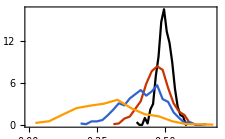

```mathematica
pltZacAlphas=ListLinePlot[histDatLst⟦1;;4⟧,PlotStyle->colorLst,Frame->True,FrameLabel->xyHistLabs,BaseStyle->texStyle,ImageSize->8cm,PlotRangePadding->None,PlotLegends->LineLegend[legLstAlpha,LegendLabel->legLabAlpha,Spacings->Small]]
```

```mathematica
Export[fNameFun["zacAvg",attrLstBaseDim~Join~{"alpha"},{nDim,mSize,divLst,itNum,seed,NumberForm[#,{2,1}]&/@alphaLst},fMod,pdfType,True],pltZacAlphas]
```

zacAvg_dim_3_N_10_param_divide_80_80_80_instanceNum_500_seed_1000_alpha_0_0.4_0.6_0.8_1.0.pdf

```mathematica
zacTmp=readJuliaVar[fNameFun["zacAvgArr",attrLst,valLst,fMod,jld2Type],"zacAvgArr"];
```

```mathematica
fNameFun["zacAvgArr",attrLst,valLst,fModAlpha,jld2Type]
```

zacAvgArr_dim_3_N_10_param_divide_[80, 80, 80]_instanceNum_500_seed_1000_alpha_1.0.jld2

```mathematica
zacTmp//Dimensions
```

{}

```mathematica
zacTmp//Dimensions
```

{10,3,500}

```mathematica
zacAvgArrLst⟦1,1,1,1⟧
```

1.03525

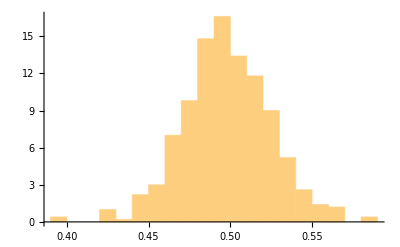

```mathematica
Histogram[zacAvgArrLst⟦All,1,4,1⟧/π,Automatic,"PDF"]
```

#### mSize plots

```mathematica
mag2dArr=Map[Mean,parity2dArr1,{2,3}]/π;
```

```mathematica
pdim=1;
```

```mathematica
n
```

4

```mathematica
xyHistLabs=MaTeX[#,Magnification->labMag]&/@{"\\bar{\\gamma}","P \\left( \\bar{\\gamma} \\right)"};
```

```mathematica
xyHistLabs
```

{-Graphics-,-Graphics-}

```mathematica
avgLab=MaTeX["\\langle \\bar{\\gamma} \\rangle = "<>ToString[NumberForm[Mean[mag2dArr⟦All,pdim,n⟧],{4,3}]],Magnification->labMag];
```

```mathematica
magHistLst=HistogramList[mag2dArr⟦All,pdim,n⟧,12,"PDF"];
```

```mathematica
magHistDat=Table[{(magHistLst⟦1⟧⟦ii⟧+magHistLst⟦1⟧⟦ii+1⟧)/2,magHistLst⟦2⟧⟦ii⟧},{ii,1,Length[magHistLst⟦2⟧]}];
```

```mathematica
magHistDat//Dimensions
```

{15,2}

```mathematica
colorLst
```

{GrayLevel[0],RGBColor[0.790588, 0.201176, 0.],RGBColor[0.192157, 0.388235, 0.807843],RGBColor[1., 0.607843, 0.],RGBColor[0., 0.596078, 0.109804],RGBColor[0.567426, 0.32317, 0.729831],RGBColor[0., 0.588235, 0.705882],RGBColor[0.8505, 0.4275, 0.13185],RGBColor[0.499929, 0.285875, 0.775177],RGBColor[0.12490296143062507, 0.63, 0.47103259454284074],RGBColor[0.823948950768196, 0.29474475384097976, 0.19291741323314934],RGBColor[0.42126358105951733, 0.33224185136428963, 0.9],RGBColor[0.7239916650994997, 0.6554435183443889, 0.],RGBColor[0.6746366424582266, 0.252, 0.45055901160272827],RGBColor[0.12582006271512805, 0.5293439498278976, 0.7809840752581536],RGBColor[0.8604677779867332, 0.4773388899336664, 0.10673699943582014],RGBColor[0.5238517042330579, 0.2719198391973829, 0.7153707394173552],RGBColor[0.37317160238437475, 0.63, 0.1550543242380685],RGBColor[0.7841372229535658, 0.23017255540928686, 0.26810462841072363],RGBColor[0.30841419880781473, 0.39995148071531117, 0.9],RGBColor[0.8969866052052705, 0.6599330260263523, 0.008136165945769741],RGBColor[0.6159549636873395, 0.252, 0.5408385174040933],RGBColor[0.01297068046342185, 0.6196234556292626, 0.6455648165561062],RGBColor[0.8378979015363919, 0.3644895076819594, 0.16083482646629865],RGBColor[0.469684000752239, 0.30351766622786064, 0.8507899981194027],RGBColor[0.5984511081857363, 0.6414945675761929, 0.],RGBColor[0.7164275936025443, 0.24371448127949116, 0.38095401066242623],RGBColor[0.19556481655611135, 0.4735481467551109, 0.8646777798673336],RGBColor[0.8744167287549299, 0.5470836437746498, 0.06907483236168915],RGBColor[0.5573291860767265, 0.2523913081219096, 0.6316770348081839],RGBColor[0.2197331439342194, 0.63, 0.35033963499281173],RGBColor[0.8153280250860514, 0.2516401254302569, 0.21274554230208187],RGBColor[0.3781589526487873, 0.35810462841072765, 0.9],RGBColor[0.8015799962388009, 0.6640644440265335, 0.],RGBColor[0.6522222356846489, 0.252, 0.4850427143313094],RGBColor[0.08271543430440877, 0.5638276525564729, 0.7292585211652906],RGBColor[0.8518468523045878, 0.4342342615229392, 0.128752239699448],RGBColor[0.5031614825959092, 0.2839891351523863, 0.767096293510227],RGBColor[0.46800178488796507, 0.63, 0.03436136468804449],RGBColor[0.7582744459071321, 0.2353451108185736, 0.3112092568214465],RGBColor[0.26530957039708464, 0.4258142577617492, 0.9],RGBColor[0.8883656795231258, 0.6168283976156295, 0.03141266528756009],RGBColor[0.5935405569137635, 0.252, 0.5753222201326715],RGBColor[0.06629468548404815, 0.63, 0.545624945747575],RGBColor[0.8292769758542473, 0.3213848792712366, 0.18066295553523118],RGBColor[0.44790370648976696, 0.3162577761061398, 0.9],RGBColor[0.6760394393250375, 0.6501154932583375, 0.],RGBColor[0.6905648165561062, 0.24888703668877876, 0.42405863907315633],RGBColor[0.1524601881453885, 0.5080318494836892, 0.8129522257744661],RGBColor[0.8657958030727825, 0.5039790153639124, 0.09235133170348728],RGBColor[0.5366389644395795, 0.26446060407691196, 0.6834025889010513],RGBColor[0.3145633264378097, 0.63, 0.2296466754427877],RGBColor[0.8001212982117243, 0.22697574035765516, 0.2414645029804596],RGBColor[0.33505432423806436, 0.3839674054571614, 0.9],RGBColor[0.8791683273781151, 0.6726853697086795, 0.],RGBColor[0.6298078289110768, 0.252, 0.519526417059882],RGBColor[0.039610805893685895, 0.5983113552850513, 0.677532967072423],RGBColor[0.8432259266224432, 0.39112963311221627, 0.14858036876838052],RGBColor[0.48247126095876225, 0.2960584311073887, 0.8188218476030944],RGBColor[0.5504988824112611, 0.6361665424901402, 0.],RGBColor[0.7324116688607027, 0.24051766622785947, 0.35431388523216223],RGBColor[0.22220494198636823, 0.4522360464109054, 0.8966459303836418],RGBColor[0.8797447538409784, 0.5737237692048922, 0.05468916462935822],RGBColor[0.571126150140184, 0.252, 0.6098059228612556],RGBColor[0.1611248679876543, 0.63, 0.42493198619753086],RGBColor[0.8206560501721027, 0.2782802508605137, 0.2004910846041637],RGBColor[0.40479907807904414, 0.34212055315257356, 0.9],RGBColor[0.7536277704643516, 0.6587364189404835, 0.],RGBColor[0.6660751009083862, 0.252, 0.46373061398709825],RGBColor[0.10935555973466561, 0.5425155522122675, 0.7612266716815987],RGBColor[0.8571748773906379, 0.4608743869531896, 0.11562783104527762],RGBColor[0.5159487428024325, 0.27652990003191436, 0.7351281429939188],RGBColor[0.4093935089414, 0.63, 0.10895371589276365],RGBColor[0.7742585211652906, 0.2321482957669419, 0.28456913139118245],RGBColor[0.29194969582734154, 0.4098301825035951, 0.9],RGBColor[0.8936937046091744, 0.6434685230458719, 0.01702699755522917],RGBColor[0.6073934221375008, 0.252, 0.5540101197884603],RGBColor[0.007686409537498939, 0.63, 0.620217296952274],RGBColor[0.8346050009402987, 0.34802500470149345, 0.16840849783731304],RGBColor[0.4617810393216153, 0.3081277270623911, 0.8705474016959619],RGBColor[0.6280872135505882, 0.6447874681722876, 0.],RGBColor[0.706548891814269, 0.2456902216371462, 0.39741851364288505],RGBColor[0.17910031357564535, 0.48671974913948374, 0.8449203762907744],RGBColor[0.8711238281588338, 0.5306191407941693, 0.07796566397114857],RGBColor[0.5494262246461028, 0.25700136895644005, 0.6514344383847431],RGBColor[0.2559550504912446, 0.63, 0.30423902664750685],RGBColor[0.8120351244899582, 0.23517562244979082, 0.22031921367309623],RGBColor[0.3616944496683212, 0.3679833301990073, 0.9],RGBColor[0.8312161016036528, 0.6673573446226281, 0.],RGBColor[0.6436606941348103, 0.252, 0.4982143167156765],RGBColor[0.06625093132394275, 0.5769992549408458, 0.7095011175887312],RGBColor[0.8485539517084946, 0.4177697585424731, 0.13632591107046238],RGBColor[0.49525852116528557, 0.2885991959869168, 0.7868536970867862],RGBColor[0.5025466566368246, 0.6308385174040916, 0.],RGBColor[0.7483957441188568, 0.23732085117622864, 0.3276737598019054],RGBColor[0.24884506741661863, 0.43569295955002885, 0.9],RGBColor[0.8850727789270298, 0.600363894635149, 0.04030349689701952],RGBColor[0.5849790153639175, 0.252, 0.5884938225170501],RGBColor[0.10251659204108926, 0.63, 0.49952433740225005],RGBColor[0.8259840752581541, 0.30492037629077057, 0.18823662690624554],RGBColor[0.431439203509301, 0.32613647789441946, 0.9]}

```mathematica
ConstantArray[0,{2,2}]
```

{{0,0},{0,0}}

```mathematica
mSzLst={10,15,20,25};
mSzLn=Length[mSzLst];
zacAvgArrLst=Table[ConstantArray[0,{itNum,nDim,mSzLst⟦mId⟧}],{mId,1,mSzLn}];
```

```mathematica
For[mId=1,mId≤mSzLn,mId++,
mSize=mSzLst⟦mId⟧;
valLstDim={nDim,mSize,divLst,itNum,seed};
zacAvgArrLst⟦mId⟧=readJuliaVar[fNameFun["zacAvgArr",attrLstDim,valLstDim,fMod,jld2Type],"zacAvgArr"];
]
```

```mathematica
fNameFun["zacAvgArr",attrLstDim,valLstDim,fMod,jld2Type]
```

zacAvgArr_dim_3_N_25_param_divide_[80, 80, 80]_instanceNum_500_seed_1000_memLayers.jld2

```mathematica
zacAvgArrLst⟦1⟧//Dimensions
```

{10,3,500}

```mathematica
histLstTmp⟦2⟧//Dimensions
```

{11}

```mathematica
binNum=20;
rat=0.4;
histDatLst=ConstantArray[0,mSzLn];
nLst=ConstantArray[0,mSzLn];
For[mId=1,mId≤mSzLn,mId++,
mSize=mSzLst⟦mId⟧;
n=Floor[rat mSize];
nLst⟦mId⟧=n;
valLstLev={nDim,mSize,divLst,itNum,seed,n};
pDim=1;
histLstTmp=HistogramList[Flatten[zacAvgArrLst⟦mId⟧⟦n,All,All⟧]/π,binNum,"PDF"];
histDatLst⟦mId⟧=Table[{(histLstTmp⟦1,ii⟧+histLstTmp⟦1,ii+1⟧)/2,histLstTmp⟦2,ii⟧},{ii,1,Length[histLstTmp⟦2⟧]}];
]
```

```mathematica
mId
```

6

```mathematica
histDatLst⟦2⟧
```

0

```mathematica
legendLst=MaTeX[ToString[#],Magnification->labMag]&/@mSzLst;
```

```mathematica
legLabel=MaTeX["M=",Magnification->labMag];
```

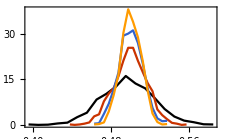

```mathematica
zacAvgMsPlt=ListLinePlot[histDatLst,PlotRange->All,PlotLegends->LineLegend[colorLst⟦1;;mSzLn⟧,legendLst,LegendLabel->legLabel,Spacings->Small],Frame->True,FrameLabel->xyHistLabs,ImageSize->8cm,PlotStyle->colorLst,BaseStyle->texStyle,PlotRangePadding->None]
```

```mathematica
Export[fNameFun["zacAvgMs",attrLstDim,[nDim,mSzLst⟦1,-1⟧,param_divide,itNum,seed},"levRat_"<>ToString[rat],pdfType,True],zacAvgMsPlt]
```

Syntax::sntxf: "fNameFun[zacAvgMs,attrLstDim," cannot be followed by "[nDim,mSzLst⟦1,-1⟧,param_divide,itNum,seed],levRat_<>ToString[rat],pdfType,True]".

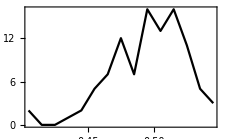

```mathematica
ListLinePlot[magHistDat,Frame->True,BaseStyle->texStyle,ImageSize->8cm,PlotStyle->colorLst⟦1⟧,PlotRangePadding->None,FrameLabel->xyHistLabs]
```

```mathematica
pltMagHist=Show[Histogram[mag2dArr⟦All,pdim,n⟧,12,"PDF",BaseStyle->texStyle,Frame->True,FrameLabel->xyHistLabs,ImageSize->8cm],Graphics[Text[avgLab,Scaled[{0.2,0.7}]]]]
```

-Graphics-

```mathematica
Export[fNameFun["magHist",attrLstDimLev,valLstLev,"",pdfType,True ],pltMagHist]
```

magHist_dim_3_N_10_param_divide_64_64_64_instanceNum_100_seed_1000_lev_4.pdf

```mathematica
valLstLev
```

{3,10,{64,64,64},100,1000,4}

## slices in only one direction

```mathematica
div=512;
```

NotebookDirectory[Notebook]

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Ohdraw.niL\Google_drive\Programming\Julia\Modules

```mathematica
filename="deg_GOE_3d_dim_2_N_4_param_divide_[512, 512]_instanceNum_1_seed_-1.jld";
```

```mathematica
posLocLst=ExternalEvaluate[sessJul,"load("<>Py[Directory[]<>"\\"<>filename]<>",\"posLocLst\")"];
```

```mathematica
Dimensions[posLocLst]
```

{512,1,5,1}

```mathematica
posLocLst⟦3,1,1⟧
```

{{{71,2},{45,5},{4,24},{60,36},{15,22},{69,30},{73,31},{18,38},{7,43},{10,78}}}

```mathematica
Flatten[posLocLst⟦3,1,1⟧,1]
```

{{71,2},{45,5},{4,24},{60,36},{15,22},{69,30},{73,31},{18,38},{7,43},{10,78}}

```mathematica
posLocLst1N4=Flatten[posLocLst⟦All,1,1⟧,1];
```

```mathematica
posLocLst1=Flatten[posLocLst⟦All,1,1⟧,1];
```

```mathematica
SortBy[posLocLst1⟦26⟧,First]
```

{{2,127},{80,130},{110,61},{152,76}}

```mathematica
posLocLst1Sorted=SortBy[#,First]&/@posLocLst1;
```

```mathematica
test//MatrixForm
```

({{57,124},{70,91}}
{{57,124},{71,90}}
{{57,124},{72,90}}
{{58,124},{73,89}}
{{58,125},{74,88}}
{{59,125},{76,87}}
{{59,125},{77,86}}
{{60,125},{78,85}}
{{60,126},{80,84}}
{{61,126},{81,83}}
{{62,127},{82,82}}
{{63,127},{84,80}}
{{63,127},{85,79}}
{{64,128},{87,78}}
{{65,128},{88,77}}
{{66,129},{90,76}}
{{67,129},{92,75}}
{{69,129},{93,73}}
{{70,130},{95,72}}
{{71,130},{97,71}}
{{72,130},{99,69}}
{{74,130},{101,68}}
{{3,93},{6,110},{75,130},{103,66}}
{{5,116},{77,131},{105,65},{160,86}}
{{4,121},{78,130},{108,63},{156,81}}
{{2,127},{80,130},{110,61},{152,76}}
{{82,130},{113,60},{141,153},{148,70}}
{{84,130},{117,58},{134,152},{142,65}}
{{87,130},{124,56},{127,149},{134,58}}
{{90,131},{120,145}}
{{94,131},{113,140}}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{}
{{3,112},{4,100}}
{{4,116},{6,98}}
{{4,120},{12,96}}
{{5,123},{21,95},{70,102},{77,97}}
{{6,126},{28,96},{65,105},{80,95}}
{{7,129},{25,8},{30,13},{33,96},{62,107},{82,93}}
{{7,132},{20,3},{34,16},{38,97},{60,109},{83,92}}
{{8,136},{17,159},{37,18},{41,99},{58,110},{84,91}}
{{9,140},{14,155},{38,20},{45,100},{57,111},{85,90}}
{{39,21},{47,101},{57,112},{86,89}}
{{40,22},{49,101},{57,113},{87,88}}
{{41,23},{51,102},{56,114},{89,88}}
{{41,23},{52,102},{56,115},{90,87}}
{{42,24},{52,103},{56,116},{91,86}}
{{43,24},{53,103},{56,116},{93,86}}
{{43,24},{53,103},{56,117},{95,85}}
{{44,24},{53,104},{56,118},{97,84}}
{{44,25},{54,104},{56,118},{100,84}}
{{45,25},{54,104},{56,119},{104,83}}
{{45,25},{54,104},{56,119},{111,82}}
{{46,25},{54,105},{56,120},{141,87}}
{{46,25},{55,105},{56,120},{144,88}}
{{46,25},{55,105},{56,121},{146,89}}
{{47,25},{55,106},{56,121},{147,90}}
{{47,24},{55,106},{57,122},{148,91}}
{{48,24},{55,106},{57,122},{149,92}}
{{48,24},{55,106},{57,123},{149,92}}
{{49,24},{56,107},{57,123},{150,93}}
{{49,24},{56,107},{57,124},{150,94}}
{{50,24},{56,107},{57,124},{150,94}}
{{50,23},{56,107},{58,125},{151,95}}
{{50,23},{56,108},{58,126},{151,96}}
{{51,23},{57,108},{58,126},{151,96}}
{{51,23},{57,108},{58,127},{151,97}}
{{52,22},{57,108},{59,127},{151,98}}
{{52,22},{57,108},{59,128},{151,98}}
{{52,22},{57,109},{59,128},{151,99}}
{{53,22},{58,109},{59,129},{151,99}}
{{53,21},{58,109},{60,129},{151,100}}
{{54,21},{58,109},{60,130},{151,101}}
{{54,21},{58,109},{60,131},{150,102}}
{{54,21},{58,109},{60,131},{150,103}}
{{55,20},{58,109},{61,132},{149,103}}
{{55,20},{59,109},{61,132},{149,105}}
{{55,20},{59,109},{61,133},{148,106}}
{{55,20},{59,109},{61,134},{146,108}}
{{56,19},{59,109},{62,134},{135,112}}
{{56,19},{59,109},{62,135},{125,108}}
{{56,19},{59,109},{62,135},{119,106}}
{{56,19},{59,108},{62,136},{114,105}}
{{56,19},{59,108},{62,137},{110,104}}
{{56,19},{60,108},{63,137},{107,103}}
{{57,18},{60,108},{63,138},{104,103}}
{{57,18},{60,108},{63,138},{101,103}}
{{57,18},{60,107},{63,139},{98,102}}
{{57,18},{60,107},{63,139},{95,102}}
{{57,18},{60,107},{63,140},{93,103}}
{{56,18},{60,107},{63,140},{90,103}}
{{56,18},{60,106},{63,141},{88,103}}
{{56,19},{60,106},{63,141},{86,103}}
{{56,19},{59,106},{63,141},{83,103}}
{{56,19},{59,105},{63,141},{81,103}}
{{55,19},{59,105},{63,141},{79,104}}
{{55,19},{59,105},{62,142},{77,104}}
{{55,20},{58,104},{62,141},{74,104}}
{{54,20},{58,104},{62,141},{72,104}}
{{54,21},{57,103},{62,141},{70,104}}
{{1,4},{1,149},{53,21},{56,103},{62,141},{68,104}}
{{2,7},{3,145},{53,21},{54,102},{61,141},{67,104}}
{{3,9},{4,142},{52,22},{52,101},{61,140},{65,103}}
{{4,12},{5,139},{49,99},{51,23},{61,140},{64,103}}
{{5,13},{6,136},{46,98},{51,23},{60,139},{64,103}}
{{6,15},{7,133},{42,96},{50,24},{60,139},{63,102}}
{{7,17},{8,131},{38,95},{49,25},{60,138},{63,102}}
{{8,18},{9,128},{31,94},{48,25},{59,137},{62,101}}
{{9,20},{10,125},{18,97},{47,26},{59,137},{62,101}}
{{10,22},{11,122},{15,101},{46,27},{58,136},{62,101}}
{{12,23},{12,119},{14,105},{45,28},{58,135},{62,100}}
{{13,25},{43,28},{58,134},{62,100}}
{{15,26},{41,29},{57,133},{62,100}}
{{16,28},{39,30},{57,132},{62,99}}
{{19,29},{37,31},{57,132},{62,99}}
{{22,31},{33,32},{57,131},{62,99}}
{{56,130},{62,98}}
{{56,129},{63,98}}
{{56,128},{63,97}}
{{56,128},{63,97}}
{{56,127},{64,96}}
{{56,126},{65,96}}
{{56,126},{65,95}}
{{56,125},{66,94}}
{{56,125},{67,94}}
{{56,125},{68,93}}
{{56,124},{69,92}})

```mathematica
posLocLst1⟦1,1⟧~Join~{1}
```

{18,37,1}

```mathematica
ptLstId=Table[Graphics3D[Point[(posLocLst1⟦id3,id1⟧~Join~{id3})]],{id3,1,Dimensions[posLocLst1]⟦1⟧},{id1,1,Dimensions[posLocLst1⟦id3⟧]⟦1⟧}];
```

```mathematica
Show[ptLstId,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]
```

-Graphics3D-

```mathematica
ptLstN4=Table[Graphics3D[Point[(posLocLst1N4⟦id3,id1⟧~Join~{id3}-1)/div]],{id3,1,Dimensions[posLocLst1N4]⟦1⟧},{id1,1,Dimensions[posLocLst1N4⟦id3⟧]⟦1⟧}];
```

```mathematica
Show[ptLstN4,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]
```

-Graphics3D-

```mathematica
ptLst=Table[Graphics3D[Point[(posLocLst1⟦id3,id1⟧~Join~{id3}-1)/div]],{id3,1,Dimensions[posLocLst1]⟦1⟧},{id1,1,Dimensions[posLocLst1⟦id3⟧]⟦1⟧}];
```

```mathematica
ptLstShX=Table[Graphics3D[Point[(posLocLst1⟦id3,id1⟧~Join~{id3}+{div,0,0}-1)/div]],{id3,1,Dimensions[posLocLst1]⟦1⟧},{id1,1,Dimensions[posLocLst1⟦id3⟧]⟦1⟧}];
```

```mathematica
ptLstShY=Table[Graphics3D[Point[(posLocLst1⟦id3,id1⟧~Join~{id3}+{0,div,0}-1)/div]],{id3,1,Dimensions[posLocLst1]⟦1⟧},{id1,1,Dimensions[posLocLst1⟦id3⟧]⟦1⟧}];
```

```mathematica
ptLstShZ=Table[Graphics3D[Point[(posLocLst1⟦id3,id1⟧~Join~{id3}+{0,0,div}-1)/div]],{id3,1,Dimensions[posLocLst1]⟦1⟧},{id1,1,Dimensions[posLocLst1⟦id3⟧]⟦1⟧}];
```

```mathematica
Show[{ptLst,ptLstShX,ptLstShY,ptLstShZ},Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->{{0,1.2},{0,1.2},{0,1.2}}]
```

-Graphics3D-

```mathematica
Show[ptLst,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]
```

```mathematica
Show[ptLst,Axes->True,AxesLabel->{"k_1","k_2","k_3"},PlotRange->Full]
```

-Graphics3D-

```mathematica
Show[ptLst,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Dimensions[posLocLst1,1]
```

{80}

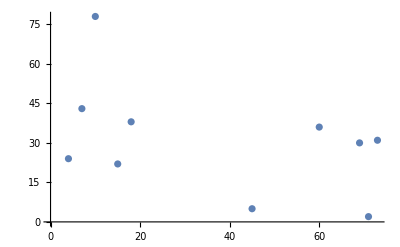

```mathematica
ListPlot[Flatten[posLocLst⟦3,1,1⟧,1]]
```

```mathematica
Flatten[posLocLst⟦All,1,1⟧,1]
```

{{{18,37},{4,43},{8,77},{44,3},{16,22},{6,23},{65,36},{72,80}},{{72,1},{45,4},{15,22},{9,78},{5,23},{62,36},{18,37},{6,43}},{{71,2},{45,5},{4,24},{60,36},{15,22},{69,30},{73,31},{18,38},{7,43},{10,78}},{{71,2},{45,5},{15,22},{77,30},{58,35},{3,25},{65,27},{18,39},{9,44},{11,79}},{{45,6},{63,24},{56,34},{71,3},{14,23},{18,40},{10,44},{12,80}},{{71,5},{63,17},{14,24},{54,33},{17,42},{13,1},{45,7},{11,44}},{{46,7},{40,16},{36,26},{52,30},{12,44},{14,2},{14,26},{11,44}},{{14,3},{46,7},{44,14},{50,22},{14,29},{31,35},{11,41},{13,45}},{{14,3},{46,7},{29,39},{13,46}},{{14,4},{47,6},{30,41},{13,47}},{{47,5},{14,4},{31,42},{12,48}},{{13,4},{47,4},{33,44},{12,49}},{{47,3},{13,4},{35,45},{11,50}},{{48,2},{12,4},{37,47},{11,51}},{{48,1},{12,4},{39,48},{10,52}},{{41,49},{10,52},{48,80},{11,3}},{{11,3},{42,50},{9,53},{49,79}},{{10,2},{43,51},{9,54},{49,78}},{{44,52},{8,54},{10,2},{50,77}},{{10,2},{45,53},{8,55},{50,77}},{{46,53},{51,76},{10,1},{7,55}},{{52,76},{10,1},{47,54},{7,56}},{{10,1},{47,54},{6,56},{52,75}},{{11,1},{53,75},{48,55},{6,56}},{{5,56},{49,55},{54,75},{11,80}},{{50,55},{55,74},{12,80},{5,56}},{{4,56},{13,80},{50,55},{56,74}},{{14,80},{51,55},{4,56},{57,74}},{{4,55},{52,55},{60,75},{67,76},{70,78},{15,80}},{{3,55},{52,55},{16,80},{71,80}},{{3,55},{71,2},{53,54},{17,80}},{{71,3},{2,54},{54,54},{18,80}},{{70,6},{1,53},{54,53},{18,79}},{{69,9},{41,11},{19,79},{42,13},{55,52},{79,52}},{{44,22},{40,4},{69,13},{57,52},{69,52},{20,79}},{{44,28},{21,79},{71,17},{46,80}},{{49,47},{21,78},{74,18},{50,78}},{{77,19},{52,78},{54,48},{22,78}},{{79,19},{53,77},{22,78},{56,48}},{{57,47},{54,77},{80,19},{22,77}},{{23,77},{1,19},{57,46},{55,77}},{{56,77},{2,19},{58,45},{23,77}},{{56,76},{3,18},{58,44},{22,76}},{{4,19},{59,43},{57,76},{22,76}},{{5,19},{60,43},{22,76},{57,76}},{{60,42},{58,75},{5,19},{22,75}},{{61,42},{22,75},{58,75},{6,19}},{{62,42},{22,74},{59,74},{6,19}},{{62,42},{7,19},{21,74},{59,74}},{{7,19},{63,43},{60,73},{21,74}},{{7,20},{64,43},{21,73},{60,73}},{{64,43},{21,73},{8,20},{61,72}},{{65,44},{21,72},{8,20},{61,72}},{{20,72},{62,72},{8,21},{65,44}},{{66,45},{20,71},{9,21},{62,71}},{{9,21},{67,45},{20,71},{62,71}},{{9,22},{67,46},{20,70},{63,70}},{{67,47},{63,70},{9,22},{19,69}},{{68,47},{18,68},{9,23},{63,70}},{{9,23},{68,48},{63,70},{17,67}},{{68,49},{24,61},{16,66},{64,69},{10,23},{17,59}},{{10,23},{68,49},{14,59},{27,63},{15,66},{64,69}},{{12,59},{29,65},{64,69},{10,24},{68,50},{14,65}},{{12,65},{31,67},{64,70},{10,24},{68,51},{11,58}},{{9,57},{11,66},{31,70},{64,70},{10,24},{68,51}},{{67,52},{6,55},{64,70},{31,72},{11,24},{10,66}},{{2,52},{66,52},{65,71},{11,24},{7,43},{5,44},{10,67},{31,74}},{{65,52},{9,68},{11,24},{10,41},{65,71},{31,75}},{{11,40},{31,76},{11,24},{63,53},{8,68},{65,72}},{{12,39},{61,54},{32,77},{11,24},{7,69},{65,72}},{{44,70},{32,78},{11,24},{13,39},{7,70},{66,73}},{{14,38},{44,72},{11,24},{6,71},{67,74},{32,80}},{{33,1},{14,37},{6,72},{11,24},{44,73},{67,75}},{{33,2},{15,37},{5,72},{44,75},{11,24},{68,75}},{{33,3},{15,37},{21,21},{20,22},{10,24},{5,73},{44,76},{69,76}},{{18,22},{16,36},{33,4},{24,19},{9,24},{5,74},{44,77},{70,77}},{{33,6},{27,18},{17,22},{9,23},{70,77},{44,78},{17,36},{5,74}},{{33,8},{17,22},{17,36},{28,16},{8,23},{6,75},{71,78},{44,79}},{{44,1},{32,11},{31,12},{32,12},{17,36},{80,42},{6,76},{31,13},{16,22},{7,23},{76,40},{71,79}},{{44,2},{71,37},{7,76},{16,22},{6,23},{18,37},{3,42},{72,79}}}

```mathematica
posLocLst⟦1,1,1⟧
```

{{{18,37},{4,43},{8,77},{44,3},{16,22},{6,23},{65,36},{72,80}}}

```mathematica
Py[Directory[]<>"\\\\"<>filename]
```

"D:\\Ohdraw.niL\\Documents\\\\deg_GOE_3d_dim_2_N_5_param_divide_[80,80]_instanceNum_1_seed_-1.jld"

```mathematica
ExportString[Directory[],"PythonExpression"]
```

"D:\\Ohdraw.niL\\Documents"